### Naloga 1

```mathematica
trikotnik =Trikotnik[{0,0}, {5,1}, {7,4}]

Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}

Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}

SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}

SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }

NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
SlikaOglisc[trikotnik]
```

{Point[{0,0}],Point[{5,1}],Point[{7,4}]}

```mathematica
SlikaStranic[trikotnik]
```

{Line[{{0,0},{5,1}}],Line[{{5,1},{7,4}}],Line[{{7,4},{0,0}}]}

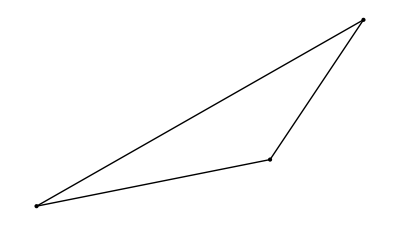

```mathematica
NarisiTrikotnik[trikotnik]
```

### Naloga 2

```mathematica
Dolzina[Daljica[AA_,BB_]] := Norm[BB -AA]
```

```mathematica
VelikostKota[Kot[AA_,BB_,CC_]]:=ArcCos[(AA-BB).(CC-BB)/(Norm[AA-BB] Norm[CC-BB])]
```

```mathematica
koti = Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
alfa = First[koti]
```

Kot[{7,4},{0,0},{5,1}]

```mathematica
VelikostKota[alfa]
```

ArcCos[3/(√10)]

```mathematica
VektorSimetraleKota[Kot[AA_,BB_,CC_],dol_]:=Normalize[Normalize[AA-BB]+Normalize[CC-BB]]*dol
```

```mathematica
VektorSimetraleKota[alfa, 1]
```

{(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2)),(1/(√26)+4/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))}

```mathematica
PresecisceSimetraleKota[Kot[AA_,BB_,CC_]] := Module[{resitev, t},
resitev = Solve[BB + k VektorSimetraleKota[Kot[AA,BB,CC], 1] == CC + 
t(AA - CC), { k, t} ]//First;
t = t/. resitev;
CC + t(AA-CC)
]
```

```mathematica
ClearAll[k]
```

```mathematica
alfa
```

Kot[{7,4},{0,0},{5,1}]

```mathematica
PresecisceSimetraleKota[alfa] //N
```

{5.77485,2.16228}

```mathematica
SlikaSimetrale[Kot[AA_,BB_,CC_]] := Line[{BB, PresecisceSimetraleKota[Kot[AA,BB,CC]]}]
```

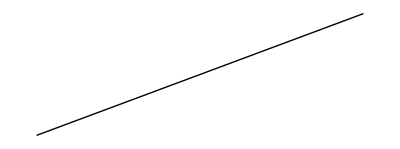

```mathematica
Graphics@SlikaSimetrale[alfa]
```

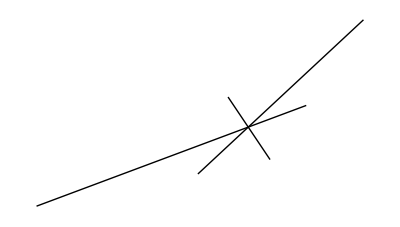

```mathematica
Graphics@Map[SlikaSimetrale, koti]
```

```mathematica
SlikaSimetralKotov[trikotnik_Trikotnik]:= Map[SlikaSimetrale, Koti[trikotnik]]
```

```mathematica
SlikaSimetralKotov[trikotnik]//Graphics
```

-Graphics-

```mathematica
NarisiTrikotnikSSimetralami[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t], SlikaSimetralKotov[t]}, AspectRatio->Automatic, PlotRange->{{-7, 10},{0, 6}}]
```

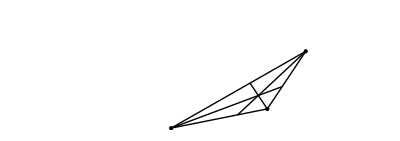

```mathematica
NarisiTrikotnikSSimetralami[trikotnik]
```

```mathematica
Manipulate[NarisiTrikotnikSSimetralami[Trikotnik[{0,0}, {5,1}, {cx,cy}]], {cx, -7, 7}, {cy, 3,6}]
```